## Funkcijske vrste

## Fourierova vrsta

Za razvoj funkcij v trigonometrične vrste ima Mathematica vgrajene funkcije.

```mathematica
?FourierSeries
?FourierTrigSeries
?FourierSinSeries
?FourierCosSeries
```

Vse funkcije privzemajo, da funkcije razvijamo na intervalu (-π,π). Razvoj na intervalu (-T/2,T/2) dobimo tako, da v ukaz dodamo opcijo FourierParameters→{1,(2π)/T}.

```mathematica
f=x^2+x;
FourierSeries[f,x,5]
FourierTrigSeries[f,x,5]
```

1. Funkcijo    f(x)={   0 ,  -π<x<0
x ,     0<x<π
razvijte v
  a.  Fourierovo  vrsto na intervalu  (-π,π)
b.  sinusno Fourierovo  vrsto na intervalu  (0,π)
c.  kosinusno Fourierovo  vrsto na intervalu  (0,π)

Narišite grafe delnih vsot vrst (upoštevajte indekse do n=10) na intervalu (-π,π) in primerjajte grafe z grafom funkcije  y=f(x).

```mathematica
If[0<x<π,x,0]
```

Funkcijo zlepljeno iz dveh formul se da zapisati z ukazom If[]    če maš dva,če maš več: Which[] ali Piecewise[].

```mathematica
f=If[0<x<Pi, x,0]
n=10;
F= FourierTrigSeries[f,x,n]
Plot [{f,F},{x,-Pi,Pi}]
```

```mathematica
Fs=FourierSinSeries[f,x,n]
Plot[{f,Fs},{x,-Pi,Pi}]
Fc=FourierCosSeries[f,x,n]
Plot[{f,Fc},{x,-Pi,Pi}]
n
```

2. Funkcijo f(x)=x+(2x)/(|x|)razvijte v Fourierjevo vrsto na intervalu (-3,3) do členov z indeksi n=12.
Skicirajte graf funkcije in graf Fourierjevega približka na intervalu (-6,6).

```mathematica
f=x+2x/Abs[x];
n=12
F = FourierTrigSeries[f,x,n,FourierParameters ->{1,2 Pi /6 }] (* parameters {1,2 Pi/ perioda} *)
Plot[{f,F},{x,-6,6}]
```

3. KOT DEMONSTRACIJA: V datoteki ekg.txt so shranjeni podatki srčnega utripa (EKG meri napetost v mV), prvi podatek je časovni korak (v sekundah).
(a) Iz podatkov izluščite le podatke za vsako stotinko za nekaj utripov in jih izrišite z ukazom ListPlot.
(b) Iz teh podatkov sestavite funkcijo f(x) z ukazom ListInterpolate.
(c) Razvijte funkcijo f(x) v Furierovo vrsto, pri čemer upoštevajte 50 členov (konstantni čeln ter 50 sinusov in 50 kosinusov). Uporabite ukaz za numeričen izračun Fourierove vrste NFourierTrigSeries, ki je del paketa FourierSeries`.
(d) Na istem grafu izrišite utrip in Fourierovo vrsto. Izrišite tudi graf napake.

```mathematica
Clear[utrip,dt,l,time,m,M,f,perioda,podatki]
(* nalozimo datoteko s podatki *)
utrip=Import[StringJoin[NotebookDirectory[],"ekg.txt"],"List"]
(* preberemo časovni korak in količino podatkov *)
dt=First[utrip];
l=Length[utrip];
(* iz podatkov izberemo le podatke za vsako stotinko na nekem segmentu (nekaj utripov) *)
utrip=Take[utrip,{1501,5501,10}];
(* popravimo časovni korak in izračunamo celoten čas *)
dt=dt*10;
l=Length[utrip];
time=l*dt;
(* izrišemo podatke na simetričen interval *)
podatki=ListPlot[utrip,DataRange->{-time/2,time/2},AspectRatio->1/4,PlotRange->All,PlotStyle->PointSize[0.005],ImageSize->800]
```

```mathematica
(* razberemo razpon vrednosti v podatkih - minumum in maksimum *)
M=Max[utrip]+1;
m=Min[utrip]-1;
(* iz diskretnih podatkov sestavimo zvezno funkcijo (interpolacija), za definicijsko območje izberemo isti interval kot prej *)
f=ListInterpolation[utrip,{{-time/2,time/2}}];
(* narišemo utrip *)
Plot[f[x],{x,-time/2,time/2},AspectRatio->1/4,PlotRange->{m,M},ImageSize->800]
```

```mathematica
(* določimo dolzino periode (enega utripa) *)
FindPeaks[utrip,0,0,2.8] (* poišče vrhove v podatkih, ki so večji od 2.8 *)
perioda=(%[[3,1]]-%[[2,1]])*dt
(* nalozimo paket za numeričen izračun Fourierove vrste in izračunamo Fourierovo vrsto *)
Needs["FourierSeries`"]
fourier=NFourierTrigSeries[f[x],x,50,FourierParameters->{1,2π/perioda}]//Simplify
```

```mathematica
(* graf utripa in Fourierove vrste *)
Plot[{f[x],fourier},{x,-perioda/2,perioda/2},AspectRatio->1/2,PlotRange->{m,M},PlotStyle->{Blue,Green},ImageSize->500]
(* graf utripa in Fourierove vrste *)
Plot[{f[x],fourier},{x,-time/2,time/2},AspectRatio->1/4,PlotRange->{m,M},PlotStyle->{Blue,Green},ImageSize->800]
```

## Dodatne naloge

4. preverjanje!!!!!

Funkcijo f(x)=sin(x), ki je podana na intervalu (0,π),sodo nadaljujte na interval (-π,0) ter tako dobljeno funkcijo razvijte v kosinusno Fourierovo vrsto na intervalu (-π,π).
Rezultat: f(x)=π/4+(∑^∞)_(k=1)2/(π(2k-1)^2)cos((2k-1)x).

```mathematica
Clear[x]
f=Sin[Abs[x]];
n=20;
Plot[f,{x,-Pi,Pi}]
FourierCosSeries [f,x,n]
```

5. malo bolj programerska

V datoteki zvok.txt so shranjeni podatki zvočnega signala (odmik tlaka od atmosferskega tlaka merjeno v Pa) za vsake 0.2 sekunde. Zvočni signal je mešanica zvoka več različnih harmonično usklajenih frekvenc. Ugotovite katere so te frekence in kakšne amplitude jim pripadajo na naslednji način:
(a) Izrišite zvočni signal na simetričnem intervalu in določite njegovo osnovno periodo.
(b) Iz podatkov sestavite funkcijo in jo razvijte v Fourierovo vrsto. Uporabite ukaz za numeričen izračun vrste in upoštevajte 15 členov razvoja.
(c) Določite vse frekvence, ki sestavljajo dani zvočni signal, in pripadajoče amplitude. Pomagajte si z ukazom Chop.
(d) Primerjajte grafa podatkov in Fourierove vrste, tako da jih prikažete na isti sliki.

```mathematica
Clear[zvok,dt,cas,perioda,z,Z,F]
zvok=Import[StringJoin[NotebookDirectory[],"zvok.txt"],"List"];
dt=0.2;
cas=Length[zvok]*dt;
ListPlot[zvok,DataRange->{-cas/2,cas/2}]
FindPeaks[zvok,0,0,50]
perioda=(%[[2,1]]-%[[1,1]])*dt
```

```mathematica
z=ListInterpolation[zvok,{{-cas/2,cas/2}}];
Needs["FourierSeries`"]
Z=NFourierTrigSeries[z[x],x,15,FourierParameters->{1,2π/perioda}]//Simplify
```

```mathematica
F=Chop[Z,0.1]
```

```mathematica
Show[
Plot[F,{x,-cas/2,cas/2}],
ListPlot[zvok,DataRange->{-cas/2,cas/2},PlotStyle->Red]
]
```

```mathematica
Naloga:
```

```mathematica
Clear[a,n]

a[n_]=(n^2)/6^n
R=Limit[a[n]/a[n+1],n->Infinity]//N
```

6^-n n^2

6.

```mathematica
Clear[x]
```

0.126988

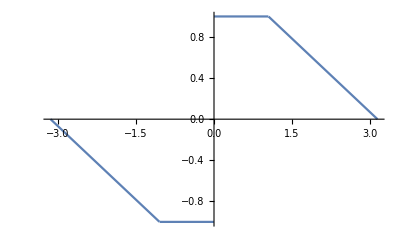

```mathematica
Clear[x]
function= Piecewise[{{-3x/(2*Pi)-3/2,-Pi/3> x},{-1, -Pi/3< x≤ 0},{1, 0< x≤ Pi/3}, {-3x/(2*Pi)+3/2, Pi/3< x}}];
FourierTrigSeries[function,x,1] /.x-> 3//N
Plot[function,{x,-Pi,Pi}]
```

```mathematica
Clear[x]
4*Normal[Series[(1+x)^(1/3),{x,0,3}]]/.x-> (-1/64)//N
```

3.97906

```mathematica
Clear[x,n]
a[n_]=n*((-1x)^n)
Sum[a[n],{n,1,Infinity}]/.x-> 1/2//N
```

```mathematica
f=If[0≤ x<Pi/3, 4,0]
n=16;
F= FourierCosSeries[f,x,n]
```

If[0≤x<π/3,4,0]

4/3+(4 √3 Cos[x])/π+(2 √3 Cos[2 x])/π-(√3 Cos[4 x])/π-(4 √3 Cos[5 x])/(5 π)+(4 √3 Cos[7 x])/(7 π)+(√3 Cos[8 x])/(2 π)-(2 √3 Cos[10 x])/(5 π)-(4 √3 Cos[11 x])/(11 π)+(4 √3 Cos[13 x])/(13 π)+(2 √3 Cos[14 x])/(7 π)-(√3 Cos[16 x])/(4 π)

```mathematica
Clear[x,n]
a[n_]=n*((n-1)*x^(n-2))
Sum[a[n],{n,1,Infinity}]/.x-> 1/3//N
```

(-1+n) n x^(-2+n)

6.75

Piecewise[{{2, π/4>x>-π/4}, {8/3-(8 x)/(3 π), π/4<x}, {8/3+(8 x)/(3 π), -π<x<π/4}, {0, True}}]

0.336746

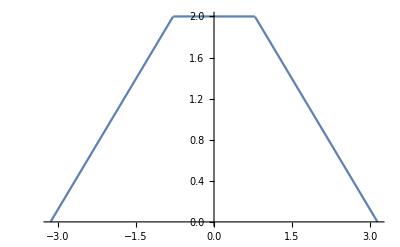

-Graphics-

```mathematica
Clear[x]
function= Piecewise[{{2,Pi/4> x>-Pi/4},{-8x/(3*Pi)+8/3, Pi/4< x}
,{8x/(3*Pi)+8/3, -Pi< x<Pi/4}}]
FourierTrigSeries[function,x,1] /.x-> 3//N
Plot[function,{x,-Pi,Pi}]
```

```mathematica
f=If[0≤ x≤ Pi/3, 3,0]
n=7;
F= FourierCosSeries[f,x,n]//N
```

If[0≤x≤π/3,3,0]

1.+1.65399 Cos[x]+0.826993 Cos[2. x]-0.413497 Cos[4. x]-0.330797 Cos[5. x]+0.236284 Cos[7. x]

```mathematica
Clear[x,n]
a[n_]=((-1)^(n)*x^(2n+2))/((2n+1)(2n+2))
Sum[a[n],{n,0,Infinity}]/.x-> 1/2//N
```

((-1)^n x^(2+2 n))/((1+2 n) (2+2 n))

0.120252

```mathematica
Clear[a,n,x]

a[n_]=(n^2/6^n )
R=Limit[a[n]/a[n+1],n->Infinity]
```

6^-n n^2

6

2

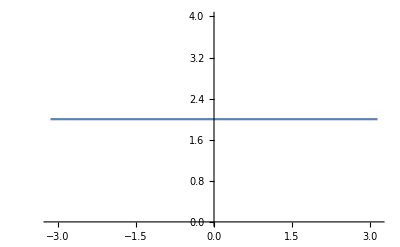

(8 Sin[x])/π+(8 Sin[3 x])/(3 π)+(8 Sin[5 x])/(5 π)+(8 Sin[7 x])/(7 π)+(8 Sin[9 x])/(9 π)+(8 Sin[11 x])/(11 π)

```mathematica
f=2
Plot[f,{x,-Pi,Pi}]
n=11;
F= FourierSinSeries[f,x,n]
```

3 Sin[x]

Sin[3 x]

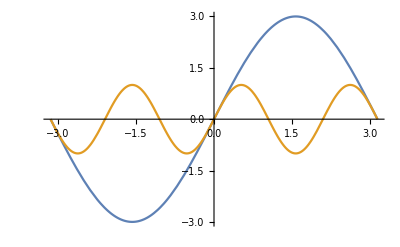

```mathematica
a=3*Sin[x]
b=Sin[3 x]
Plot[{a,b},{x,-Pi,Pi}]
```

```mathematica
Clear[x]
```

```mathematica
a[x_]=(3((Sin[x/7])-x/7))/(2x^3)
Limit[(3((Sin[x/7])-x/7))/(2x^3),x->0]
Limit[a[x],x->0]
```

Set::write: Tag Times in (3 Sin[x])[x_] is Protected.

(3 (-x/7+Sin[x/7]))/(2 x^3)

-1/1372

lim_(x→0) (3 Sin[x])[x]

```mathematica
Integrate[Sin[x/2]/x,{x,0,2}] //N
Integrate[(1-Cos[x/3])/x,{x,0,1}] //N
```

0.946083

0.0276495

Piecewise[{{-6-(6 x)/π, x<-(5 π)/6}, {-1, -(5 π)/6<x<0}, {1, 0<x<(5 π)/6}, {6-(6 x)/π, x>(5 π)/6}, {0, True}}]

1.04725

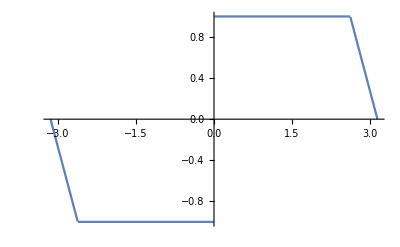

```mathematica
Clear[x]
function= Piecewise[{{(-6x)/Pi-6,x<(-5Pi/6)},{-1, (-5Pi/6)< x<0}
,{1, 0< x<5Pi/6}, {(-6x)/Pi+6,x>(5Pi/6)}}]
FourierTrigSeries[function,x,1] /.x-> 1//N
Plot[function,{x,-Pi,Pi}]
```

```mathematica
Clear[x,n]

a[n_]=(2+n)*x^(n+1) 
Sum[a[n],{n,0,Infinity}]/.x-> 1/3//N
```

(2+n) x^(1+n)

1.25